1

1

1/x^3-x

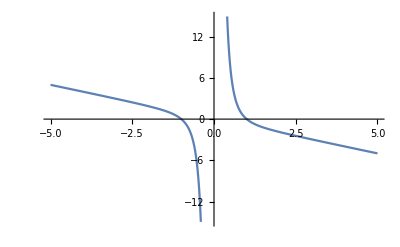

```mathematica
(* The force *)
a = 1
k = 1
Fx = -k*x + a/x^3
Plot[Fx, {x, -5,5}]
```

```mathematica
(* The potential energy *)
Ux = Integrate[-Fx,x]
```

1/(2 x^2)+x^2/2

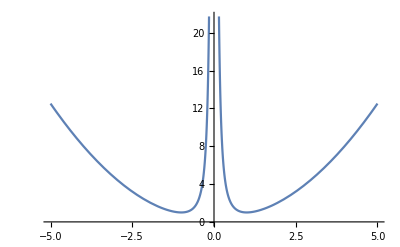

```mathematica
Plot[Ux,{x,-5,5}]
```

```mathematica
(* Total energy *)
m = 1
v = Dt[x,t]
Et = (1/2)*m*v^2 + Ux
```

1

Dt[x,t]

1/(2 x^2)+x^2/2+1/2 Dt[x,t]^2